```mathematica
Px0[x_,σ0_]=1/(√(2 π σ0^2))ⅇ^(-x^2/(2 σ0^2));


Pv0[v_,vth_]=1/(√(2 π vth^2))ⅇ^(-v^2/(2 vth^2));
P0[x_,v_,σ0_,vth_]= Px0[x,σ0]Pv0[v,vth];
V0[x_,σ0_]=Integrate[D[FullSimplify[-Log[Px0[x,σ0]],Assumptions->{σ0>0}],x],x]
```

Piecewise[{{1/(-a+b), a<x<b}, {0, True}}]

0

```mathematica
P
```

```mathematica
Solve[x-v0 t -t v==a,v]
```

{{v→(-a-t v0+x)/t}}

```mathematica
Pxslice[x_,t_,σ0_,vth_,v0_,a_,b_]=FullSimplify[
Pv0[0,vth]Px0[0,σ0]Integrate[ⅇ^(-( v^2/(2 vth^2)+V0[(x-(v+v0)t), σ0])),{v,-v0+(x-b)/t,-v0 +(x-a)/t},
Assumptions->{σ0>0,vth>0,t>0,b>a, v0>0}] ,Assumptions->{σ0>0,vth>0,t>0,b>a}]
```

(ⅇ^(-(-t v0+x)^2/(2 (t^2 vth^2+σ0^2))) (-Erf[(a t^2 vth^2+(a+t v0-x) σ0^2)/(√2 t vth σ0 √(t^2 vth^2+σ0^2))]+Erf[(b t^2 vth^2+(b+t v0-x) σ0^2)/(√2 t vth σ0 √(t^2 vth^2+σ0^2))]))/(2 √(2 π) √(t^2 vth^2+σ0^2))

```mathematica
FullSimplify[1/(2 π vth σ0)Integrate[ⅇ^(-( v^2/(2 vth^2)+ (x-t(v+v0))^2/(2 σ0^2))),{v,-v0+(x-b)/t,-v0 +(x-a)/t},
Assumptions->{σ0>0,vth>0,t>0,b>a, v0>0}] ,Assumptions->{σ0>0,vth>0,t>0,b>a}]
```

```mathematica
FullSimplify[Pxslice[x,t,σ0,vth,J g vth,-∞,-(2 J +1)δ σ0]+
Pxslice[x,t,σ0,vth,-J g vth,(2 J +1)δ σ0,∞],
Assumptions->{σ0>0,vth>0,α>0, β>0,t>0,g>0, δ>0, mJ ∈Reals, J>1}]
```

1/(2 √(2 π) √(t^2 vth^2+σ0^2))ⅇ^(-(g^2 J^2 t^2 vth^2+x^2)/(t^2 vth^2+σ0^2)) (ⅇ^((g J t vth+x)^2/(2 (t^2 vth^2+σ0^2))) (1+Erf[(-((1+2 J) t^2 vth^2 δ)+g J t vth σ0-σ0 (x+δ σ0+2 J δ σ0))/(√2 t vth √(t^2 vth^2+σ0^2))])+ⅇ^((-g J t vth+x)^2/(2 (t^2 vth^2+σ0^2))) Erfc[((1+2 J) t^2 vth^2 δ-(g J t vth+x) σ0+(1+2 J) δ σ0^2)/(√2 t vth √(t^2 vth^2+σ0^2))])

```mathematica
FullSimplify[Pxslice[x,t,σ0,vth,v0,a, b],
Assumptions->{σ0>0,vth>0,α>0, β>0,t>0,γ>0, δ>0, mJ ∈Reals, J>1}]
```

(ⅇ^(-(-t v0+x)^2/(2 (t^2 vth^2+σ0^2))) (-Erf[(a t^2 vth^2+(a+t v0-x) σ0^2)/(√2 t vth σ0 √(t^2 vth^2+σ0^2))]+Erf[(b t^2 vth^2+(b+t v0-x) σ0^2)/(√2 t vth σ0 √(t^2 vth^2+σ0^2))]))/(2 √(2 π) √(t^2 vth^2+σ0^2))

```mathematica
Integrate[ⅇ^(-(a-y)^2/2) Erf[(y/(√2)) ],{y,-∞, ∞}, Assumptions->{b>a,vth>0,σ0>0}]
```

Integrate[ⅇ^(-1/2 (a-y)^2) Erf[y/(√2)],{y,-∞,∞},Assumptions→{b>a,vth>0,σ0>0}]

```mathematica
Integrate[(σ0 α)^2(ⅇ^(-(α+mJ β γ)^2/(2 (1+β^2))) (Erf[(α+mJ β γ-(-1+2 mJ) (1+β^2) δ)/(√2 β √(1+β^2))]+Erf[(-α-mJ β γ+(1+2 mJ) (1+β^2) δ)/(√2 β √(1+β^2))]))/(2 √(2 π) √(1+β^2) σ0),{α,-∞,∞}, Assumptions->{γ>0,β>0,mJ∈Reals,δ>0,σ0>0}]
```

Integrate[(ⅇ^(-(α+mJ β γ)^2/(2 (1+β^2))) α^2 σ0 (Erf[(α+mJ β γ-(-1+2 mJ) (1+β^2) δ)/(√2 β √(1+β^2))]+Erf[(-α-mJ β γ+(1+2 mJ) (1+β^2) δ)/(√2 β √(1+β^2))]))/(2 √(2 π) √(1+β^2)),{α,-∞,∞},Assumptions→{γ>0,β>0,mJ∈ℝ,δ>0,σ0>0}]

```mathematica
FullSimplify[Pxslice[x σ0,t σ0/vth,σ0,vth,v0 vth,a σ0,b σ0], Assumptions->{t>0, σ0>0, vth>0, γ>0, δ>0 ,vth>0}]
```

(ⅇ^(-(-t v0+x)^2/(2 (1+t^2))) (-Erf[(a+a t^2+t v0-x)/(√2 t √(1+t^2))]+Erf[(b+b t^2+t v0-x)/(√2 t √(1+t^2))]))/(2 √(2 π) √(1+t^2) σ0)

```mathematica
Integrate[Erf[a x+b] ⅇ^((-(x-μ)^2)/(2 σ^2)),{x,-∞,∞}, Assumptions->{a>0,b>0, c>0,μ>=0,σ>0}]
```

Integrate[ⅇ^(-(x-μ)^2/(2 σ^2)) Erf[b+a x],{x,-∞,∞},Assumptions→{a>0,b>0,c>0,μ≥0,σ>0}]

```mathematica
Solve[α+mJ γ-2 δ-4 mJ δ==y,α]
```

{{α→y-mJ γ+2 δ+4 mJ δ}}

```mathematica
Manipulate[Show[Plot[Px0[x,1],{x,-5,5}],Plot[Pxslice[x,t,1,1*^-6,10,x0-∞,x0+0.5],{x,-5,5},PlotRange->{Automatic,{0,17}}]],{t,1*^-21,1},{x0,-1,1}]
```

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

General::munfl: Exp[-1.01241×10^55] is too small to represent as a normalized machine number; precision may be lost.

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

General::munfl: Exp[-9.22658×10^54] is too small to represent as a normalized machine number; precision may be lost.

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::munfl: Exp[-8.37073×10^54] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Sqrt[12.]
```

3.4641

```mathematica
Pcenter[x_,t_,σ0_,vth_,J_,δ_,γ_]:=FullSimplify[
Sum[Pxslice[x,t,σ0,vth,-mJ γ vth,2 mJ δ σ0-δ σ0 ,2 mJ δ σ0+δ σ0 ],{mJ,-J+1,J-1,1}] ,Assumptions->{σ0>0,vth>0,t>0,γ>0 ,δ>0 ,J>0}]
Pedges[x_,t_,σ0_,vth_,J_,δ_,γ_]:=FullSimplify[
Pxslice[x,t,σ0,vth,J γ vth,-2J  δ σ0-∞ ,-2J  δ σ0+δ σ0 ]+
Pxslice[x,t,σ0,vth,-J γ vth,2J  δ σ0-δ σ0 ,2J  δ σ0+∞ ],Assumptions->{σ0>0,vth>0,t>0,γ>0 ,δ>0 }]
Ptotal[x_,t_,σ0_,vth_,J_,δ_,γ_]:=FullSimplify[Pcenter[x,t,σ0,vth,J,δ,γ]+Pedges[x,t,σ0,vth,J,δ,γ],Assumptions->{σ0>0,vth>0,t>0,γ>0 ,δ>0 }]

Ptable[x_,t_,σ0_,vth_,J_,δ_,γ_]:=FullSimplify[
Join[{Pxslice[x,t,σ0,vth,-2J  δ σ0,J γ vth,-∞ ,δ σ0 ],
Pxslice[x,t,σ0,vth,2J  δ σ0,-J γ vth,-δ σ0 ,∞ ]},
Table[Pxslice[x,t,σ0,vth,2 mJ δ σ0,-mJ γ vth,-δ σ0 ,δ σ0 ],{mJ,-J+1,J-1,1}]] ,Assumptions->{σ0>0,vth>0,t>0,γ>0 ,δ>0 ,J>0}]
```

```mathematica
ListPtable[t_,σ0_,vth_,J_,δ_,γ_]:=Transpose[Table[{x,Ptable[x,t,σ0,vth,J,δ,γ]⟦i⟧},{x,-5,5,0.05},{i,1,3,1}]]
```

```mathematica
Manipulate[Show[Plot[Ptotal[x,t,1,1,2,δ,γ],{x,-5,5}],ListPlot[ListPtable[t,1,1,1,δ,γ]],PlotRange->{Automatic,{0,1}}],{t,1*^-21,1},{δ,1*^-21,2},{γ,1*^-21,10}]
```

```mathematica
varslice[x_,t_,σ0_,vth_,x0_,v0_,a_,b_]=Integrate[
x^2 Pxslice[x,t,1,1,x0,0,a,b],{x,x0+a,x0+b},
Assumptions->{σ0>0,vth>0,t>0,b>a,x0>0,v0>0}]
```

$Aborted

```mathematica
Pxslice[x,t,1,1,x0,0,a,b]
```

(ⅇ^(-x^2/(2 (1+t^2))) (-Erf[(a-x+x0+t^2 (a-2 x+x0))/(√2 t √(1+t^2))]+Erf[(b-x+x0+t^2 (b-2 x+x0))/(√2 t √(1+t^2))]))/(2 √(2 π) √(1+t^2))

```mathematica
Integrate[ⅇ^(-1/2 M v^2/kBT),{v,-∞,∞}]
```

ConditionalExpression[(√(2 π))/(√(M/kBT)), Re[M/kBT]>0]

```mathematica
var[δ_,J_]:=Integrate[x^2 Piecewise[{{Px0[x+2 J δ,1], x<-δ}, {Sum[Px0[x-2 mJ δ,1],{mJ,-J,J}], -δ<=x<=δ}, {Px0[x+2 J δ,1], x>δ}}],{x,-∞,∞}]
```

```mathematica
var[δ_,J_]:=1 - 4 δ Sum[√(2/π)Exp[(-δ^2(2 mJ+1)^2)/2]-δ(mJ + 1)Erfc[(δ(2 mJ+1))/(√2)],{mJ,0,J-1}]
```

```mathematica
Solve[-4J √(2/π)+4J(J+1)δ-6 √(2/π)J^2 δ^2==0,δ]//Simplify
```

{{δ→((1+J) √π+√(2 J (-6+π)+π+J^2 π))/(3 √2 J)},{δ→((1+J) √π-√(2 J (-6+π)+π+J^2 π))/(3 √2 J)}}

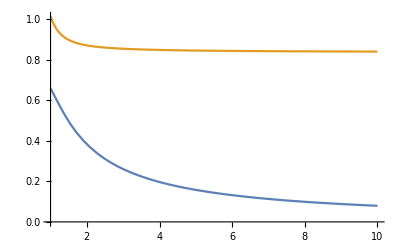

```mathematica
Plot[{((1+J) √π-√(2 J (-6+π)+π+J^2 π))/(3 √2 J),((1+J) √π+√(2 J (-6+π)+π+J^2 π))/(3 √2 J)},{J,1,10}]
```

```mathematica
Table[Series[D[var[δ,J],δ],{δ,0,1}]//FullSimplify,{J,1,5}]
```

{-4 √(2/π)+8 δ+O[δ]^2,-8 √(2/π)+24 δ+O[δ]^2,-12 √(2/π)+48 δ+O[δ]^2,-16 √(2/π)+80 δ+O[δ]^2,-20 √(2/π)+120 δ+O[δ]^2}

```mathematica
Solve[D[Series[var[δ,4],{δ,0,1}],δ]==0,δ]
```

{}

```mathematica
FullSimplify[var[δ,1],Assumptions->{δ>0}]//Apart
```

(ⅇ^(-(9 δ^2)/2) δ)/(√(2 π))-(5 ⅇ^(-δ^2/2) δ)/(√(2 π))+1/2 (2+8 δ^2+Erf[δ/(√2)]-4 δ^2 Erf[δ/(√2)]+Erf[(3 δ)/(√2)]+4 δ^2 Erf[(3 δ)/(√2)])

```mathematica
FullSimplify[var[δ,2],Assumptions->{δ>0}]//Apart
```

-4 ⅇ^(-δ^2/2) √(2/π) δ+(3 ⅇ^(-(25 δ^2)/2) δ)/(√(2 π))-(3 ⅇ^(-(9 δ^2)/2) δ)/(√(2 π))+1/2 (2+32 δ^2-8 δ^2 Erf[δ/(√2)]+Erf[(3 δ)/(√2)]-8 δ^2 Erf[(3 δ)/(√2)]+Erf[(5 δ)/(√2)]+16 δ^2 Erf[(5 δ)/(√2)])

```mathematica
FullSimplify[var[δ,3],Assumptions->{δ>0}]//Apart
```

-4 ⅇ^(-(9 δ^2)/2) √(2/π) δ-4 ⅇ^(-δ^2/2) √(2/π) δ+(5 ⅇ^(-(49 δ^2)/2) δ)/(√(2 π))-(ⅇ^(-(25 δ^2)/2) δ)/(√(2 π))+1/2 (2+72 δ^2+Erf[(5 δ)/(√2)]+Erf[(7 δ)/(√2)]+8 δ^2 Erfc[δ/(√2)]+24 δ^2 Erfc[(3 δ)/(√2)]+4 δ^2 Erfc[(5 δ)/(√2)]-36 δ^2 Erfc[(7 δ)/(√2)])

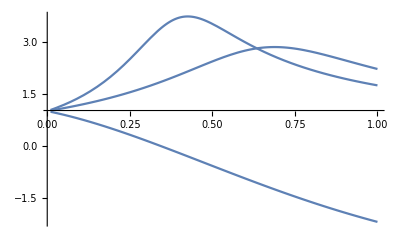

```mathematica
Show[Plot[1/√(-ⅇ^(-(9 δ^2)/2) √(2/π) δ-ⅇ^(-δ^2/2) √(2/π) δ+Erf[δ/(√2)]+Erfc[(3 δ)/(√2)]+4 δ^2 Erfc[(3 δ)/(√2)]),{δ,0.01,1}],
Plot[1/√(-3 ⅇ^(-(25 δ^2)/2) √(2/π) δ+ⅇ^(-(9 δ^2)/2) √(2/π) δ-4 ⅇ^(-δ^2/2) √(2/π) δ-4 δ^2 Erf[δ/(√2)]+Erf[(3 δ)/(√2)]+4 δ^2 Erf[(3 δ)/(√2)]+Erfc[(5 δ)/(√2)]+16 δ^2 Erfc[(5 δ)/(√2)]),{δ,0.01,1}],Plot[1-4δ Sum[√(2/π)ⅇ^(-(2 mJ+1)^2/2)+δ(2 mJ+1)Erfc[(δ(2 mJ+1))/(√2)],{mJ,0,1-1}],{δ,0.01,1}], PlotRange->Full]
```